# Honours Research Project Fractional Calculus

## Under supervision of Dr. A Swartz by FJ Wessels 217 000 643

Department of Pure and Applied Mathematics
University of Johannesburg
2017 - 2018

## Historical Overview

In the early stages of fractional calculus, interpolation problems and extending formulae domains played a crucial role.

Fractional calculus has its origin in a letter to L’Hopital from Leibniz in 1695.

In this letter he suggests d^(1/2)x=x √(d x) - What could √(d x)possibly mean?

Circa 1814 Cauchy derived the complex integral formula

	f^(n)(z) =(n!)/(2π ⅈ)∮(f(ξ))/(ξ-z)^(n+1)dξ	as a consequence of the Cauchy-Goursat theorem.

La Croix (1819) used Euler's (1729) gamma function

Γ(z)=∫_0^∞ t^(z-1) e^-t ⅆt		and		Γ(1/2)=√π 	to derive		d^(1/2)/(d x^(1/2))x=2 √(x/π)		and 		d^(1/2)/(d x^(1/2))x^0=1/(√(π x))		(not 0)

In 1832, Niels Hendrik Abel solved the tautochrone problem using fractional calculus (discussed later)

Circa 1847 Riemann and Liouville extended the n-fold (n ϵ ℂ) Repeated Cauchy integral formula to

f^(-n)(x)=1/(Γ(n))∫_c^x (x-t)^(n-1)f(t)ⅆt                 (Notice Γ(n)  is undefined at poles-1,-2,-3,...)

The history of fractional calculus extends over 300 years, yet new advances are being made daily (also discussed later)

## Question

Interpolation formulae for        	···∫∫∫ f ⟵ ∫∫ f ⟵ ∫ f ⟵ f ⟶ f'⟶ f''⟶ f'''···

Are there intermediate steps between these n - fold integral and differential operations?

## Preliminaries (Spoken Definitions)

Local and non-local operator

We call the (integer order) differential operator a local operator since traditionally, the behaviour of the differential operator applied to a function at a certain point, is determined only by what happens with the function values in an arbitrarily small neighbourhood about this point.

The integral and non-integer order differential operators are non-local (global) operators. This means, to determine the behaviour of such operators applied to a function at a certain point, we need information about values of the function “far” from that point (or “missing/transient/initial” information) - this is basically the motivation for the integration constant. 

Why do we need these concepts?

In order to understand the Riemann-Liouville, and other formulations for the fractional calculus, we must notice first that differentiation and integration are not necessarily inverse operators and that non-local properties apply.

Let’s define what we mean by inverse operator

## Definition (Linear Operator)

Let X be a vector space. A linear operator T,  is a mapping T:D ( T )→R ( T ) where D ( T ) ⊂  X, such that
 
1) The domain D ( T ) of T is a vector space and the range R ( T ) of T lies in a vector space over the same scalar field

2) for all x and y in D ( T ) and scalars α, we have

		i)   T ( x + y ) = T x + T y		and		ii)   T (α  x ) = α  T ( x )

## Definition (Left and Right Inverse Operators)

Let T be defined as before and Let  I : D ( T ) →  D ( T ) be the identity operator on D ( T ) ⊂  X. Then

1) if there exists an operator  S : R ( T ) →  D ( T )  such that for all x ϵ  D ( T ) ;  ( S ∘  T )(  x  )  = I x  then S is said to be the left inverse operator of T
(Their Composition is an Identity Element with S on the Left)

2) if there exists an operator  Q : R ( T ) →  D ( T )  such that for all x ϵ  D ( T ) ;  ( T ∘  Q )(  x  )  = I x  then Q is said to be the right inverse operator of T
(Their Composition is an Identity Element with S on the Right)

Composition

Denote by D_a^n f and D_a^-n f the n-fold derivative and integral of a function f based at point a respectively

We see it fit to mention (without proof), in the integer order case n, m ϵ  ℕ , that the following composition laws (exponent laws) for differentiation and integration hold

1) D_a^n D_a^m= D_a^(n+m)												(Derivative Composition)

2) D_a^n D_a^-m= D_a^(n-m)												(Derivative First n > m)

3) D_a^-n D_a^-m= D_a^(-n-m)=D_a^(-(n+m))										(Integral Composition)

4) D_a^-n D_a^m= D_a^(-n+m)	if and only if	0=f(a)=f'(a)=f''(a)=f'''(a)=..		(Integration First)		

Notice that the Laplace transform of the derivative behaves in a similar way as formula 4’s conditional (Transient Terms)

We are interested in the particular case, no. 4

We exclaim that formula 4 motivates various developments for the fractional derivative as discussed next.
It turns out that the fractional derivative behaves a lot like an integral operator.

This info about the operators lead to an interesting result.

“If the derivative operator lies to the left of the integral operator, the integration terms vanish. If the derivative lies to the right of the integral, we get things such as series expansion - Discussed later.

## Key Ideas

## Riemann-Liouville Formalism

The Riemann-Liouville formalism is our main interest in the project and starts by defining the fractional integral operator first then defining the fractional derivative from it.

This has the advantages of:

“avoiding differentiation first” which is more difficult to study. So it becomes the building block for developing ideas in the subject later.

avoids computations of the undefined expression Γ (p), where p is any complex pole of the Gamma function, so that the Riemann-Liouville fractional integral is well-defined.

```mathematica
A few comments on notation and definitions:
```

## Definition (Riemann-Liouville Fractional Integral)

Let Ω = [ a , b ] where  -∞ < a < b < ∞  be a finite closed interval on the real axis. The left sided and right sided Riemann-Liouville Fractional Integrals of order α  based at a and b, respectively, are given by 

(“left and right sided” not to be confused with the previous discussion)

J_(a+)^αf(x)=1/(Γ(α))∫_a^x (x-t)^(α-1)f(t)ⅆt	x > a ; Re(α  )> 0	(Left Sided Riemann-Liouville Integral Operator)*

J_(b-)^αf(x)=1/(Γ(α))∫_x^b (t-x)^(α-1)f(t)ⅆt	x < b ; Re(α  )> 0	(Right Sided Riemann-Liouville Integral Operator)

Here we used J^α instead of D^-α and J^α serves as an extension of the Cauchy formula for repeated integrals

Next, we look at the derivative.

## Definition (Riemann-Liouville Fractional Derivative)

The left-sided and right sided Riemann-Liouville fractional derivatives of order α  based at a and b, respectively, is defined in terms of the fractional integral:  

D_(a+)^αf(x)=(ⅆ/ⅆx)^m[D_(a+)^(-(m-α))f(x)]=(ⅆ/ⅆx)^m[J_(a+)^(m-α)f(x)]			x > a

D_(b-)^αf(x)=(-ⅆ/ⅆx)^m[D_(b-)^(-(m-α))f(x)]=(-ⅆ/ⅆx)^m[J_(b-)^(m-α)f(x)]		x < b

where m is the nearest integer greater than α  i.e. m=Ceiling[α], sometimes written as m - 1 < α  < m

Notice that we placed the integer-order derivative operator first, followed by the fractional integral operator.

We often omit subscripts if the context of discussion is clear and simply write D^αf(x)

## Example (Notation)

To compute the 1/3-derivative and 4/3-derivative of a function f, we are forced to write

D^(1/3)f(x)=D^1 D^(-2/3)f(x)

D^(4/3)f(x)=D^2 D^(-2/3)f(x)

Notice (as mentioned before)

Fractional integration is performed first before integer-order differentiation.

This definition avoids computations of the undefined expression Γ (p), where p is any complex pole of the Gamma function, so that the Riemann-Liouville fractional integral is well-defined.

## Example (La Croix - Particular Case)

The semi-derivative D^(1/2) of functions f(t)=t

Let us start by considering the more general case t^λ for arbitrary α ϵ  ℂ and

ⅆ^α/(ⅆ t^α)t^λ=D^m[J^(m-α)t^λ]
	=D^m[(Γ( λ + 1 ))/(Γ( λ + m - α + 1 ))t^(λ + m - α)]
	=(Γ ( λ + 1 ))/(Γ ( λ - α + 1 ))t^(λ - α) 
															
Now, we substitute α=1/2 and λ=1 to obtain

D^(1/2)t=(Γ ( 1 + 1 ))/(Γ ( 1 - 1/2 + 1))t^(1 - 1/2)=2 √(t/π)

Interestingly, if we apply the semi-derivative again, we obtain the expected result

D^(1/2)D^(1/2)t=2/(√π)D^(1/2)√t=2/(√π)(Γ ( 1/2 + 1 ))/(Γ ( 1/2 - 1/2 + 1 ))t^(1/2-1/2)=2/(√π)(√π)/2=1

## Properties of Riemann-Liouville Differ-Integral Operator

We need Linearity for the next example so we state some properties of the differ-integral operator

1) (J^α)(J^β f)(x)=(J^(α+β)f)(x)						(semi-group property for fractional integral)

2) J^α(λ f (x) + μ g (x) )=λ J^α f(x) + μ J^α g(x)			(linearity for fractional integral)

3) (D^α)(D^β f)(x)=(D^(α+β)f)(x)						(semi-group property for fractional derivative)

4) D^α(λ f (x) + μ g (x) )=λ D^α f(x) + μ D^α g(x)			(linearity of fractional derivative)	

The proof of properties 3 and 4 follow from that of properties 1 and 2 and the properties of the integer-order differential operator

Proof of linearity property 2 is straight forward.

### Outline of proof for property 1.

We write the expression for (J^α J^β f)(x) using the definition of the Riemann-Liouville integral operator.

(J^α J^βf)(x)=1/(Γ(α)Γ(β))∫_a^x ∫_a^t (x-t)^(α-1)(t-s)^(β-1)f(s)  ⅆs  ⅆt	where the double integral is taken over the region R={(s,t)|a≤s≤t  and  a≤t≤x}

Next, we change the order of integration to obtain

(J^αJ^βf)(x)=1/(Γ(α)Γ(β))∫_a^x ∫_s^t (x-t)^(α-1)(t-s)^(β-1)f(s)  ⅆs  ⅆt	where the region is now expressible as R'={(s,t)|s≤t≤x  and  a≤s≤t}

We then introduce the change of variables t=s+(x-s)r

After manipulation and use of the beta function, we arrive at our result

(J^α J^βf)(x)=1/(Γ(α+β))∫_a^x (x-s)^(α+β-1)f(s)  ⅆs  =(J^(α+β)f)(x)

## Example (La Croix - Limit)

The semi-derivative D^(1/2) of functions f(t)=c where c is an arbitrary constant

Again, we use the more general case ⅆ^α/(ⅆ t^α)c t^λ=c(Γ(λ+1))/(Γ(λ-α+1))t^(λ-α) and then apply the limit as λ→0

D^α c =lim_(λ→0) D^α c t^λ=clim_(λ→0) (Γ(λ+1))/(Γ(λ-α+1))t^(λ-α)=c/(Γ(1-α))t^-α

## Variations

We would like to demonstrate, although not elaborate, that equally suitable alternative formalisms for the fractional calculus exists


Let us suppose that the Riemann-Liouville fractional derivative is defined from the fractional integral by replacing α, the order of integration, by -α to denote differentiation.

D^αf(x)=J^-α f(x)=1/(Γ(-α))∫_a^x (x-t)^(-α-1)f(t)ⅆt		(This is similar to the Weyl (1917) differ-integral)


We reconcile this approach with the Cauchy Integral formula from complex analysis

Starting with	ⅆ^n/(ⅆ z^n)f(z) =(n!)/(2π ⅈ)∮_C (f(ξ))/(ξ-z)^(n+1)dξ		where C is a closed contour surrounding point z and enclosing a region of analyticity of f

We replace the positive integer n by a non-integer q, so that (ξ-z)^(-q-1) no longer has a pole at ξ=z, but a branch point so that we can define in the quadrant Re(ξ) ≤0   and   Im(ξ)≤0

ⅆ^q/(ⅆ z^q)f(z) =(Γ( q + 1 ))/(2π ⅈ)∮_C (f(ξ))/(ξ-z)^(q + 1)dξ	;	q not a negative integer

where contour C begins and terminates at ξ=0.


we will need the symmetry formula for the gamma function

Γ( z ) Γ( 1 - z ) =π/(sin ( z π ))  for   0<Re( z )<1, z not an integer and replacing z by q + 1 to get 

Γ( q + 1) Γ( - q ) =π/(sin ( ( q  + 1 ) π )) ⟶  Γ( q + 1) =π/(- sin ( q π )Γ( - q ))


We deform the contour to obtain an appropriate (Hankel) contour C' about the point z and introduce the change of variables (ξ-z) ⟶ (ξ-z)  e^(2iz) so that


ⅆ^q/(ⅆ z^q)f(z) =(Γ( q + 1 ))/(2π ⅈ)(1-e^(-2π i ( q + 1 )))∫_0^z (f(ξ))/(ξ-z)^(q + 1)dξ

	      = Γ(q+1)e^(-π i ( q + 1 ))/π(e^(π i ( q + 1 )) - e^(- π i ( q + 1 )))/(2  ⅈ)∫_0^z (f(ξ))/(ξ-z)^(q + 1)dξ

	      = Γ(q+1)e^(-π i (q+1))/π sin( ( q + 1 ) π )∫_0^z (f(ξ))/(ξ-z)^(q + 1)dξ

	      = Γ(q+1)( - 1 )^(-q-1)/π sin( ( q + 1 ) π )∫_0^z (f(ξ))/(ξ-z)^(q + 1)dξ

	      =π/(sin ( ( q + 1 ) π ) Γ( - q ))( - 1 )^(-q-1)/π sin( ( q + 1 ) π )∫_0^z (f(ξ))/(ξ-z)^(q + 1)dξ

	     =1/(Γ( - q ))∫_0^z (f(ξ))/(ξ-z)^(q + 1)dξ                       Provided   Re ( q )<0

This is exactly the formula above with lower limit of integration a=0

## Laplace Transform

We would like to demonstrate how the Laplace transform is useful in the fractional calculus

We can use the property of the convolution product for the Laplace transform

ℒ{ f ( t ) * g ( t ) }=ℒ{ f ( t ) }ℒ{ g ( t ) }

to establish a relationship for the Riemann-Liouville fractional integral which is given by J^α f(x)=ℒ^-1{s^-α ℒ{f(t)}} which can provide us with a shortcut for deriving interpolation formulae

## Example (Use of Laplace)

J^α f( x )=ℒ^-1{ s^-α ℒ{ t^k } }=ℒ^-1{(Γ ( k + 1 ))/s^(α + k + 1)}=(Γ ( k + 1 ))/(Γ(  α + k + 1 ))t^(α + k)		where α + k > -1

## Grünwald-Letnikov Formalism

In contrast to the Riemann-Liouville formalism which derives a differ-integral from repeated integration, Grünwald-Letnikov derives a differ-integral from repeated differentiation.

The classical definition of the derivative is given by 

f'(x)=lim_(h→0) (f( x + h ) - f( x ))/h

by applying this definition to f'(x) we obtain

f''(x)=lim_(h→0) (f'( x + h ) - f'( x ))/h=lim_(h→0) (lim_(h→0) (f( x + h +h) - f( x+h ))/h - lim_(h→0) (f( x + h ) - f( x ))/h)/h=lim_(h→0) (f( x + 2h ) -  2f(x+h)  +  f( x ))/h^2

Recursively, after n differentiations, we obtain the formula

ⅆ^n/(ⅆ x^n)f(x)=lim_(h→0) 1/h^n∑_(m=0)^n (-1)^m(n
m)  f( x - m h )

This definition is generalized to non-integer values for n provided we substitute the binomial coefficients with their gamma coefficients and the upper limit of summation n goes to infinity as (t-a)/hwhere t and a are the upper and lower limits of differentiation.

ⅆ^q/(ⅆ x^q)f(x)=lim_(h→0) 1/h^q∑_(m=0)^((t-a)/h) (-1)^m(Γ( q + 1 ))/(m! Γ(q - m +1 ))f( x - m h )

Similarly, the fractional order Grünwald-Letnikov integral is derived by replacing q  by -q to obtain 

ⅆ^(- q)/(ⅆ x^(- q))f(x)=lim_(h→0) h^q∑_(m=0)^((t-a)/h) (-1)^m(Γ( q + m ))/(m! Γ( q ))f( x - m h )

Remarks:

It can be shown that the Grünwald-Letnikov formalism is equivalent to the Riemann-Liouville formalism (however the proof is quite lengthy and won’t be discussed)

The Grünwald-Letnikov formulation lends itself readily to numerical methods

## Caputo Formalism

Recall that the Riemann-Liouville derivative was defined

D^αf(x)=(ⅆ/ⅆx)^m[D^(-(m-α))f(x)]=(ⅆ/ⅆx)^m[J^(m-α)f(x)]		where the integer order derivative is applied second which produces transient terms

and m is the nearest integer greater than α  i.e. m=Ceiling[α], sometimes written as m - 1 < α  < m

## Definition (Caputo Derivative)

D^αf(x)=D^(-(m-α))[(ⅆ/ⅆx)^m f(x)]=J^(m-α)[(ⅆ/ⅆx)^m f(x)]

where m is the nearest integer greater than α  i.e. m=Ceiling[α], sometimes written as m - 1 < α  < m

As a result of integration second, the transient terms become in the form of a “series”. This leads us to the next discussion of the Fractional Taylor Series.

## Fractional Taylor Series

In the definition of the Caputo derivative, we notice that the integer-order differential operator is applied to the function f first after which non-integer integration is performed.

D^αf(x)=J^(m-α)[(ⅆ/ⅆx)^m f(x)]

As mentioned before, this gives rise to the transient terms and so also gives us a clue as to how the Taylor series in fractional  calculus could be defined.

## Definition (Fractional Taylor Series)

The fractional Taylor series of a function f(x) centered about a point a is given by

f(x)=f(a)+∑_(k>0) _a J_x^k(_a D_x^kf(x))

which is equivalent to 

f(x)=f(a)+∑_(k>0)    (ⅆ^k/(ⅆ x^k)f(x))_(x=a)  (1/(Γ ( k ))∫_a^x (x-t)^(k-1)ⅆt)

since  (ⅆ^k/(ⅆ x^k)f(x))_(x=a) are constants for all k

We feel the need to mention that the term f(a) cannot be included in the summation, since the integral for k = 0  involves computation of Γ ( 0 ) which is undefined

## Example (Binomial Expansion)

To demonstrate the power of the fractional Taylor series, we expand the function f(x)=(x+y)^n about a = 0 and reconcile it with the classical form of the binomial expansion

Notice that f(0)=(0+y)^n=y^n and that (ⅆ^k/(ⅆ x^k)(x+y)^n)_(x=0)=(Γ ( n + 1 ))/(Γ ( n - k + 1 ))y^(n-k) so that we get

f(x)=y^n+∑_(k=1)^∞ (Γ ( n + 1 ))/(Γ ( n - k + 1 ))y^(n-k) (1/(Γ ( k ))∫_a^x (x-t)^(k-1)ⅆt)

         =y^n+∑_(k=1)^∞ (Γ ( n + 1 ))/(Γ ( n - k + 1 ))y^(n-k)x^k/(Γ ( k + 1 ))

         =y^n+∑_(k=1)^∞ (Γ ( n + 1 ))/(Γ ( n - k + 1 )  Γ ( k + 1 )) x^k y^(n-k)

         =y^n+∑_(k=1)^∞ (n
k)  x^k y^(n-k)

        =∑_(k=0)^∞ (n
k)  x^k y^(n-k)

which is the concise expression for the classical binomial expansion as we know it

## Example ( Exp, Sin, Cos)

We demonstrate the fractional Taylor series approximation of three fundamental functions and demonstrate that our series expansion need not be initiated at an integer number for k.

```mathematica
Manipulate[Expand[{D[E^x,{x,0}]/.{x->0}}+∑_(k=1)^n (1/Gamma[k]*∫_0^y {D[E^x,{x,k}]/.{x->0}}*(y-t)^(k-1)ⅆt)],{n,0,10,1}]
```

```mathematica
Manipulate[Expand[{D[Sin[x],{x,0}]/.{x->0}}+∑_(k=1)^n (1/Gamma[k]*∫_0^y {D[Sin[x],{x,k}]/.{x->0}}*(y-t)^(k-1)ⅆt)],{n,0,20,1}]
```

```mathematica
Manipulate[Expand[{D[Cos[x],{x,0}]/.{x->0}}+∑_(k=1)^n (1/Gamma[k]*∫_0^y {D[Cos[x],{x,k}]/.{x->0}}*(y-t)^(k-1)ⅆt)],{n,0,20,1}]
```

Up to now, k was an integer number and we expanded the terms in integer steps. We demonstrate the semi-series expansion of cos ( x )

This means that the series expansion of cos ( x ) will be initiated at k=1/2 and each new term will be obtained by counting in 1/2 steps

```mathematica
Manipulate[Expand[(D[Cos[x],{x,0}]/.{x->0})+∑_(k=1/2)^n (1/Gamma[k]*∫_0^x (Cos[x+(Pi k)/2 ]/.{x->0})*(x-t)^(k-1)ⅆt)],{n,0,20,1/2}]
```

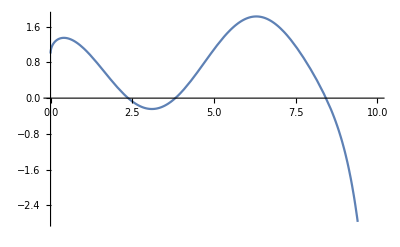

```mathematica
Plot[1+√(2/π) √x-2/3 √(2/π) x^(3/2)-4/15 √(2/π) x^(5/2)+8/105 √(2/π) x^(7/2)+16/945 √(2/π) x^(9/2)-(32 √(2/π) x^(11/2))/10395-(64 √(2/π) x^(13/2))/135135+(128 √(2/π) x^(15/2))/2027025+(256 √(2/π) x^(17/2))/34459425-(512 √(2/π) x^(19/2))/654729075-(1024 √(2/π) x^(21/2))/13749310575+(2048 √(2/π) x^(23/2))/316234143225+(4096 √(2/π) x^(25/2))/7905853580625-(8192 √(2/π) x^(27/2))/213458046676875-(16384 √(2/π) x^(29/2))/6190283353629375+(32768 √(2/π) x^(31/2))/191898783962510625+(65536 √(2/π) x^(33/2))/6332659870762850625-(131072 √(2/π) x^(35/2))/221643095476699771875-(262144 √(2/π) x^(37/2))/8200794532637891559375+(524288 √(2/π) x^(39/2))/319830986772877770815625,{x,0,10}]
```

For interest sake, we mention a quick word about the generalised power sum formula ∑_(n=1)^n i^k

k=0           ⟹          ∑_(n=1)^n i^k=n+1

k=1          ⟹          ∑_(n=1)^n i^k=(n( n + 1 ))/2

k=2         ⟹          ∑_(n=1)^n i^k=(n( n + 1 )( 2 n + 1 ))/6

and so we are interested in an interpolation formula to generalise this power sum. Euler’s operator (x d/(d x)) has been used to establish

∑_(n=1)^n i^k=lim_(x→1) (x d/(d x))^k((x^(n+1)-1)/(x-1))

We want to comment on the following formula instead

```mathematica
Manipulate[∑_(x=1)^n k*∫_0^x (x-t)^(k-1)ⅆt,{k,1,5,1}]
```

Notice the integral kernel is of the form in Riemann-Liouville’s formalism

We also want to ask whether k could be a non-integer

## Tautochrone (Isochrone Problem)

The Tautochrone problem states:

Determine the curve in the ( x , y ) -plane such that the time required for a particle with mass m, to
slide down the curve to its lowest point (ignoring friction), is a minimum, independent of its initial
placement on the curve


( X , Y ) is the initial placement of the particle
( 0 , 0 ) is the final placement of the particle
( x , y ) is the intermediate placement of the particle
σ  is the arc length measured from the origin ( 0 , 0 )
m is the mass of the particle
g  is the gravitational acceleration constant
t  is the independent variable time


By the conservation of energy law from classical physics

The gain in kinetic energy is equal to the loss of the potential energy

In symbols this becomes

1/2 m ((d σ)/(d t))^2=m g ( Y-y )

d σ=-√(2  g ( Y-y ))d t                             since           (d σ)/(d t)<0        (arclength decreases as particle slides down)

d σ=(d σ)/(d y)  d y					(chain rule)

let  σ^(1)(y)=(d σ)/(d y) then we obtain the separable ODE

 (σ^(1)(y))/(√(Y - y))=-√(2 g)d t

Integrating from y=Y to y=0 on the left and corresponding t_Y=0 and t_0=T we get the convolution form

 y^(-1/2)*σ^(1)=√(2 g)  T

Applying the Laplace transform, we obtain Abel’s solution of the Tautochrone problem

σ(y)=1/π∫_0^y (f ( Y ))/(√(y - Y))ⅆY	where f(Y)=√(2 g)  T

We demonstrate a significantly easier method to solve this problem that avoids the use of Laplace transform and evaluating complicated integrals

starting with the semi-integral of σ^(1)

J^(1/2)σ^(1)=1/(√π)∫_0^Y (σ^(1) ( y ))/(√(Y - y)) ⅆt

Applying the semi-integral operator on both sides again immediately yields the same result 

σ(y)=1/π∫_0^y (f ( Y ))/(√(Y - y))ⅆY	where f(Y)=√(2 g)  T

## Integral Equations

## Future Directions

## Connection to Functional Analysis, Measure Theory and Fractals